## VertexCut

```mathematica
VertexCut[g_?UndirectedGraphQ,parm___]:=VertexCut[DirectedGraph[g],parm]
```

```mathematica
VertexCut[g_?MultigraphQ,parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g:Except[_?LoopFreeGraphQ],parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g_?DirectedGraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];(*I understand this line*)
m=Transpose[IncidenceMatrix[g]];(*I don't understand what this line is for I understand what the incidence matrix represents and what the transpose of a matrix represents but I don't understand what this does.*)
a=UnitStep[m-1];(*I don't understand why the unit step is being used.*)
b=a-m;(*I don't understand this either*)
res=LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorLessEqual]1(*I understand this as saying *),a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[g_?DirectedGraphQ,s_,t_] /; VertexQ[g,s]&&VertexQ[g,t]:=
Block[{res,n,m,a,b,u,v,i,j},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
i=VertexIndex[g,s];
j=VertexIndex[g,t];
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1,Indexed[u,i]==1,Indexed[u,j]==0,Indexed[v,i]==0,Indexed[v,j]==1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[RandomGraph[{5,10}]]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

{}

## Example

```mathematica
edges={start->F201,F201->Q,start->F202,F202->Q,Q->P,start->F203,F203->P,P->B21,F203->B21,start->F204,F204->B21,start->F205,F205->B21,start->F206,F206->B21,start->F207,F207->C21,C211->C21,F207->C211,C212->C21,start->C213,C213->C21,C21->B21,B21->H21,C21->H21,H21->H211,start->FH211,FH211->H211,C211->H211,H211->IH2111,IH2111->goal,start->L21,L21->C21,B21->L21,C21->D1,C212->D1,B21->D1,D1->E22,C211->E22,start->FE22,FE22->E22,E22->E221,start->FE221,FE221->E221,E22->K3123,K3123->goal,E221->MR,MR->goal,B21->G21,start->FG21T1,FG21T1->G21,start->FG21T2,FG21T2->G21,G21->G211,G211->X,X->goal,B21->K31,C21->K31,C212->K31,K31->K3111,K3111->Y,Y->goal,B21->J31,C21->J31,C211->J31,start->FJ311,FJ311->J31,start->FJ312,FJ312->J31,J31->J311,J311->goal,B21->J32,C21->J32,C211->J32,start->FJ32,FJ32->J32,J32->J321,J321->goal,B21->R201,R201->Z,Z->goal,P->T1,F204->T1,F206->T1,T1->R201,R201->AQ,AQ->goal,T1->U1,F208->U1,U1->U11,U11->RE,RE->goal,T1->U2,F208->U2,U2->U21,U21->TY,TY->goal};
```

```mathematica
g=Graph[edges];
```

```mathematica
a=VertexCut[g,start,goal]
```

{B21,H211,E22,E221,G21,K3111,J31,J32,T1}

```mathematica
Length[a]
```

9

```mathematica
VertexConnectivity[g,start,goal]
```

9

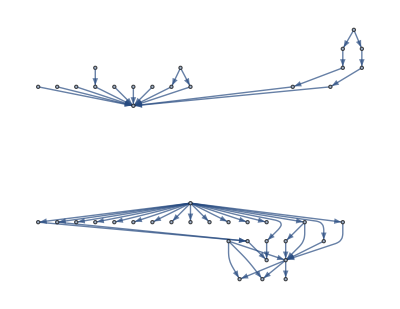

```mathematica
VertexDelete[g,a]
```